```mathematica
data1=Import["/home/jayz/Dokumente/Studium/Master/WARB/input/scripted/result1"];
data2=Import["/home/jayz/Dokumente/Studium/Master/WARB/input/scripted/result2"];
```

```mathematica
cleanData1=Cases[Drop[#,{3}]&/@data1,Except[{_,_,0}]];cleanData2=Cases[Drop[#,{3}]&/@data2,Except[{5000.,_,_}|{_,_,0}]];
```

```mathematica
cleanData=Join[cleanData1,cleanData2];
```

```mathematica
ListPlot3D[cleanData]
```

-Graphics3D-

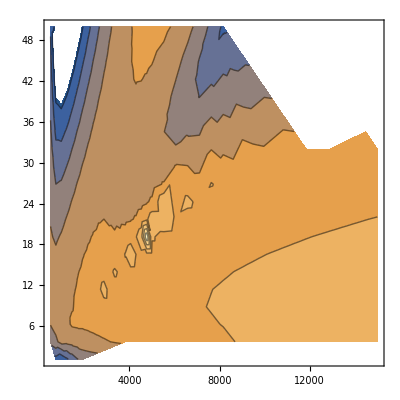

```mathematica
ListContourPlot[cleanData]
```